## Focal Point

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oranszachter/Desktop/interaction/Final/pics/untitled folder

```mathematica
Colors={RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179]};
```

```mathematica
Get["dataR2"]; (*Calculated data*)
dataR=Table[dataR⟦n⟧,{n,2,Length[dataR]}];

(*Experimental results*)
expx={3.491134358,2.754914347,2.884660308,6.393706294,4.6,8.2};
errx={0.282450548,0.198976228,0.145642723,0.599300699,0.4,0.8};
expy={0.115,0.06618275,0.103427896,0.204309988,0.171703704,0.196};
err={0.01,0.02,0.02,0.02,0.02,0.02};
plterrx=Table[Around[expx⟦n⟧,errx⟦n⟧],{n,6}];
plterr=Table[Around[expy⟦n⟧,err⟦n⟧],{n,6}];
```

```mathematica
(*ListPlot[{{dataRᵀ⟦1⟧,Limit[(dataRᵀ⟦2⟧-a)/(dataRᵀ⟦1⟧-a),a-> 1]}ᵀ,{plterrx,plterr}ᵀ},AxesLabel->{"Rout/Rin","(Stopping Point - Rin)/(Rout - Rin)"}]*)
```

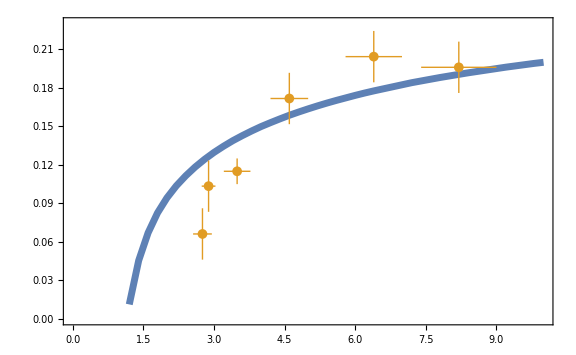

```mathematica
plt=Show[ListPlot[{dataRᵀ⟦1⟧,Limit[(dataRᵀ⟦2⟧-a)/(dataRᵀ⟦1⟧-a),a-> 1]}ᵀ(*,AxesLabel->{"Rout/Rin","(Stopping Point - Rin)/(Rout - Rin)"}*),Joined->True,PlotRange->{0,0.23},PlotStyle->{AbsoluteThickness[5]},AxesStyle->{{Thick},{Thick}},LabelStyle->{Large,Bold},Ticks->{Automatic, {0.05,0.1,0.15,0.2}},TicksStyle->{Large}],ListPlot[{plterrx,plterr}ᵀ(*,AxesLabel->{"Rout/Rin","FractionBox[(Stopping\Point-Rin),(Rout-Rin)]"},PlotStyle->Red*),PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051]},PlotMarkers->{Automatic,Medium}],Frame->True,FrameStyle->Thick,ImageSize->Large]
```

```mathematica
Export["focal.bmp",plt,"BMP"]
```

focal.bmp

## Energy Release Rate

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oranszachter/Desktop/interaction/Final/pics/fig_mathematica copy

```mathematica
engs=Table[data=ToExpression[Delete[Import[StringJoin["engs",ToString[n],".csv"]],1]];
{dataᵀ⟦4⟧,dataᵀ⟦5⟧,dataᵀ⟦1⟧ᵀ⟦1⟧,dataᵀ⟦1⟧ᵀ⟦2⟧}ᵀ,{n,1,8}];
```

```mathematica
grads=Table[T=engs⟦m⟧;
Table[
tm=T⟦n⟧;
t=T⟦n+1⟧;
tp=T⟦n+2⟧;
{t⟦1⟧,(tp⟦2⟧-tm⟦2⟧)/Sqrt[(tm⟦3⟧-tp⟦3⟧)^2+(tm⟦4⟧-tp⟦4⟧)^2]},{n,Length[T]-2}],{m,8}];
```

```mathematica
grads2=Table[T=grads⟦m⟧;
Table[
{(T⟦n,1⟧+T⟦n+1,1⟧+T⟦n+2,1⟧)/3,(T⟦n,2⟧+T⟦n+1,2⟧+T⟦n+2,2⟧)/3},{n,Length[T]-2}],{m,8}];
```

```mathematica
Colors={RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],Black};
n={0,1.5,3,4.5,6,7.5,9,-4};
n=Abs[ (n-4.5)/(1.5 4.5)];
c=Table[ColorData["Rainbow"][n1],{n1,n}];
```

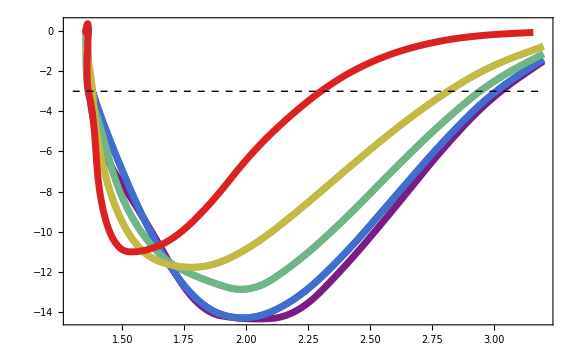

```mathematica
plt=Show[Table[ListPlot[grads⟦n⟧,Joined->True,Mesh->None,InterpolationOrder->2,PlotStyle->{c⟦n⟧,AbsoluteThickness[5]}(*,PlotLegends->{StringJoin[ToString[NumberForm[3/4+((n-1)1.5)/(2 9),{3,2}]],"π"]}*)(*,AxesLabel->{"r","G"},PlotLabel->"Energy Release Rate"*),AxesStyle->{{Thick},{Thick}},LabelStyle->{Large,Bold}],{n,Length[engs]}],Plot[-3,{x,1.3,3.2},PlotStyle->{Dashed,Thick,Black}],PlotRange->All,Frame->True,FrameStyle->Thick,ImageSize->Large]
```

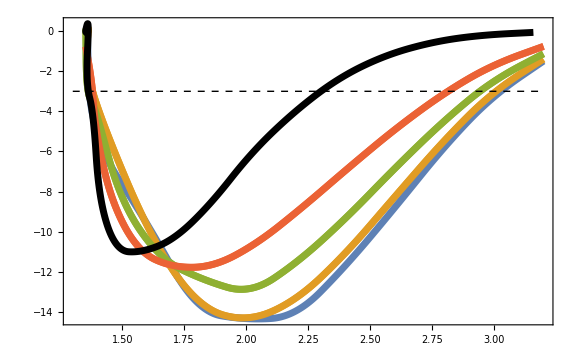

```mathematica
plt=Show[Table[ListPlot[grads⟦n⟧,Joined->True,Mesh->None,InterpolationOrder->2,PlotStyle->{Colors⟦n⟧,AbsoluteThickness[5]}(*,PlotLegends->{StringJoin[ToString[NumberForm[3/4+((n-1)1.5)/(2 9),{3,2}]],"π"]}*)(*,AxesLabel->{"r","G"},PlotLabel->"Energy Release Rate"*),AxesStyle->{{Thick},{Thick}},LabelStyle->{Large,Bold}],{n,Length[engs]}],Plot[-3,{x,1.3,3.2},PlotStyle->{Dashed,Thick,Black}],PlotRange->All,Frame->True,FrameStyle->Thick,ImageSize->Large]
```

```mathematica
Export["de.eps",plt,"EPS"]
```

de.eps

## Trails

```mathematica
Quit
```

Import data

```mathematica
SetDirectory[NotebookDirectory[]]
datadipole=Delete[ToExpression[Import["dipoledata1.csv"]],1];
```

/Users/oranszachter/Desktop/interaction/Final/pics/fig_mathematica copy

### Interpolation

Here I extract the relevant data from the calculated data

```mathematica
toInterpolateθ=Table[{datadipole⟦n,1⟧,datadipole⟦n,2⟧},{n,Length[datadipole]}];
toInterpolateE=Table[{datadipole⟦n,1⟧,datadipole⟦n,5⟧},{n,Length[datadipole]}];
toInterpolateX=Table[{datadipole⟦n,1⟧,datadipole⟦n,3,1⟧},{n,Length[datadipole]}];
toInterpolateY=Table[{datadipole⟦n,1⟧,datadipole⟦n,3,2⟧},{n,Length[datadipole]}];
```

```mathematica
fθ=Interpolation[toInterpolateθ];
fE=Interpolation[toInterpolateE];
fX=Interpolation[toInterpolateX];
fY=Interpolation[toInterpolateY];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Rout=3.7;
Rin=0.98;
Y=1;
νp=1/2;
A[ξ_,η_]:=RegionDifference[RegionDifference[Disk[{0,0},Rout],Disk[{0,0},Rin]],Disk[{ξ,η},0.1(Rout-Rin)]];
```

The trails of the cracks

```mathematica
trails2=Table[
θ=(3π)/4+(π n)/(2 9);
x=Rout Cos[θ];
y=Rout  Sin[θ];Table[
x1=x;
y1=y;
intX=fX[x,y];
intY=fY[x,y];
x=x1+1/100 intX;
y=y1+1/100 intY;
{x1,y1},{n,1000}],{n,{0,1.5,3,4.5,6,7.5,9,-4,13}}];
```

InterpolatingFunction::femdmval: Input value {-2.6163,2.6163} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {-2.60942,2.60904} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
n={0,1.5,3,4.5,6,7.5,9,-4,13};
n=Abs[ (n-4.5)/(1.5 4.5)];
c=Table[ColorData["Rainbow"][n1],{n1,n}]
```

{RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.4391281111111111, 0.7049679999999999, 0.5292500000000001],RGBColor[0.2563255555555556, 0.43092088888888885, 0.8085534444444444],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2563255555555556, 0.43092088888888885, 0.8085534444444444],RGBColor[0.4391281111111111, 0.7049679999999999, 0.5292500000000001],RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.857359, 0.131106, 0.132128]}

{RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.4391281111111111, 0.7049679999999999, 0.5292500000000001],RGBColor[0.2563255555555556, 0.43092088888888885, 0.8085534444444444],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2563255555555556, 0.43092088888888885, 0.8085534444444444],RGBColor[0.4391281111111111, 0.7049679999999999, 0.5292500000000001],RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.857359, 0.131106, 0.132128]}

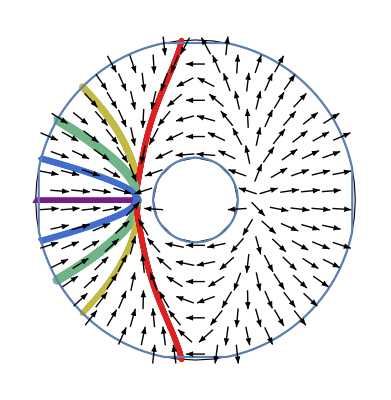

```mathematica
Show[Region[A[0,0],BaseStyle->{White,EdgeForm[{Thick,Black}]}],ListPlot[trails2,PlotMarkers->{Automatic, Small},PlotStyle->c],ListVectorPlot[{datadipoleᵀ⟦1⟧,datadipoleᵀ⟦3⟧}ᵀ,VectorPoints->15,VectorStyle->Black,VectorColorFunction->None,RegionFunction->Function[{x,y},Rin^2<x^2+y^2<Rout^2],RegionFillingStyle->None]]
```

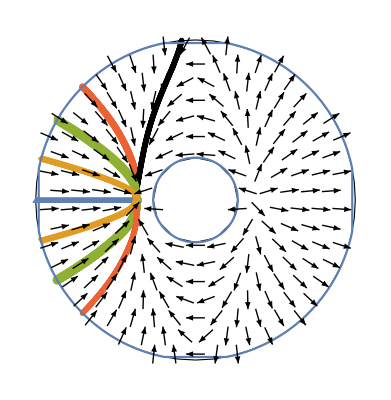

```mathematica
Show[Region[A[0,0],BaseStyle->{White,EdgeForm[{Thick,Black}]}],ListPlot[trails2,PlotMarkers->{Automatic, Small},PlotStyle->{RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],Black}],ListVectorPlot[{datadipoleᵀ⟦1⟧,datadipoleᵀ⟦3⟧}ᵀ,VectorPoints->15,VectorStyle->Black,VectorColorFunction->None,RegionFunction->Function[{x,y},Rin^2<x^2+y^2<Rout^2],RegionFillingStyle->None]]
```

#### The Displacement

```mathematica
(*ux[u_,v_]=(1br)/(2 π)(ArcTan[x,y]+1/(2(1-νp))(u v)/(u^2+v^2));
uy[u_,v_]=-(1br)/(2 π)((1-2νp)/(2(1-νp))Log[√(u^2+v^2)]+1/(2(1-νp))u^2/(u^2+v^2));*)
ϕ[Z_]=(-Z^2/(Rin^2+Rout^2)+Log[(1/Rin^2+1/Rout^2) (Z Exp[(ⅈ π)/2])])/(-8 π);
η[Z_]=-((Rin^2 Rout^2)/(Rin^2+Rout^2)+Z^2 Log[(1/Rin^2+1/Rout^2) (Z Exp[(-ⅈ π)/2])])/(8 π Z);
dis[Z_,Zbar_]:=Simplify[1/Y((3-νp)ϕ[Z]-(1+νp)(Z ϕ'[Zbar]+η'[Zbar]))];
```

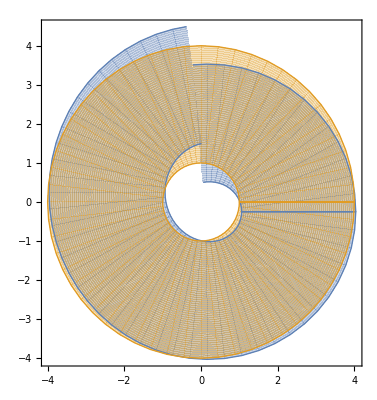

```mathematica
ParametricPlot[{{r Cos[θ]+Re[dis[r Exp[ⅈ θ],r Exp[-ⅈ θ]]],r Sin[θ]+Im[dis[r Exp[ⅈ θ],r Exp[-ⅈ θ]]]},{r Cos[θ],r Sin[θ]}},{r,1,4},{θ,0,2π}]
```

problem transforming vector field

```mathematica
dest=datadipoleᵀ⟦1⟧+datadipoleᵀ⟦3⟧;
```

1358

```mathematica
pointsm=
Table[pt=datadipoleᵀ⟦1,n⟧;
(*rp=Sqrt[pt⟦1⟧^2+pt⟦2⟧^2];
θp=ArcTan[pt];*)
Z=pt⟦1⟧+ⅈ pt⟦2⟧;
Zbar=pt⟦1⟧-ⅈ pt⟦2⟧;
pt+{Re[dis[Z,Zbar]],Im[dis[Z,Zbar]]},
{n,2,Length[datadipole]}]//N;
```

```mathematica
destm=Table[pt=dest⟦n⟧;
(*rp=Sqrt[pt⟦1⟧^2+pt⟦2⟧^2];
θp=ArcTan[pt];*)
Z=pt⟦1⟧+ⅈ pt⟦2⟧;
Zbar=pt⟦1⟧-ⅈ pt⟦2⟧;
pt+{Re[dis[Z,Zbar]],Im[dis[Z,Zbar]]},
{n,2,Length[datadipole]}]//N;
```

```mathematica
vecsm=destm-pointsm;
```

problem transforming points

```mathematica
trailsm=Table[trail=trails2⟦n⟧;
Table[
pt=trail⟦m⟧;
(*rp=Sqrt[pt⟦1⟧^2+pt⟦2⟧^2];
θp=ArcTan[pt];*)
Z=pt⟦1⟧+ⅈ pt⟦2⟧;
Zbar=pt⟦1⟧-ⅈ pt⟦2⟧;
pt+{Re[dis[Z,Zbar]],Im[dis[Z,Zbar]]},
{m,Length[trail]}],{n,Length[trails2]}]//N;
```

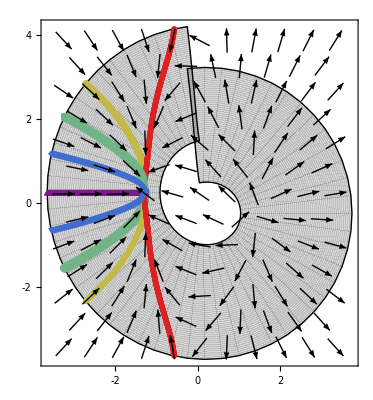

```mathematica
plt=Show[ParametricPlot[{r Cos[θ]+Re[dis[r Exp[ⅈ θ],r Exp[-ⅈ θ]]],r Sin[θ]+Im[dis[r Exp[ⅈ θ],r Exp[-ⅈ θ]]]},{r,Rin,Rout},{θ,-3π/2,1/2π},BoundaryStyle->{Thick, Black},Mesh->None,GridLines->None,PlotStyle->Gray,PlotTheme->"Business"],ListPlot[trailsm,PlotMarkers->{Automatic, Small},GridLines->None,PlotStyle->c],ListVectorPlot[{pointsm,vecsm}ᵀ,VectorPoints->11,VectorStyle->Black,VectorColorFunction->None,(*RegionFunction->Function[{x,y},{x,y}∈plotR],*)(*RegionFunction->Function[{x,y},Rin^2<(x)^2+(y)^2<Rout^2],*)RegionFillingStyle->None,GridLines->None]]
```

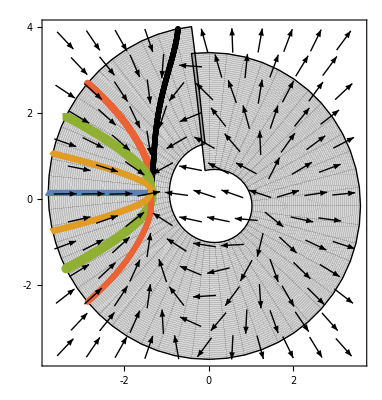

```mathematica
plt=Show[ParametricPlot[{r Cos[θ]+Re[dis[r Exp[ⅈ θ],r Exp[-ⅈ θ]]],r Sin[θ]+Im[dis[r Exp[ⅈ θ],r Exp[-ⅈ θ]]]},{r,Rin,Rout},{θ,-3π/2,1/2π},BoundaryStyle->{Thick, Black},Mesh->None,GridLines->None,PlotStyle->Gray,PlotTheme->"Business"],ListPlot[trailsm,PlotMarkers->{Automatic, Small},GridLines->None,PlotStyle->{RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],Black}],ListVectorPlot[{pointsm,vecsm}ᵀ,VectorPoints->11,VectorStyle->Black,VectorColorFunction->None,(*RegionFunction->Function[{x,y},{x,y}∈plotR],*)(*RegionFunction->Function[{x,y},Rin^2<(x)^2+(y)^2<Rout^2],*)RegionFillingStyle->None,GridLines->None]]
```

```mathematica
Export["trails.eps",plt,"EPS"]
```

trails.eps

## Principal Stresses

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

### Definition

```mathematica
ρ=(Rin Rout)/(√(Rin^2+Rout^2));
R=√(Rin^2+Rout^2);
co={u,v};
```

```mathematica
f1[u_,v_,θ_]=Y/(4π)({Cos[θ],Sin[θ]}.{u,v})(Log[(u^2+v^2)/ρ^2]+ρ^2/(u^2+v^2)-(u^2+v^2)/R^2); (*Static Dipole at the origin*)
Q[θ_]=q{{Cos[2θ],Sin[2θ]},{Sin[2θ],-Cos[2θ]}};
f2[u_,v_,θ_,ξ_,η_]:=Simplify[Y/(16 π)({u-ξ,v-η}.Q[θ].{u-ξ,v-η})/({u-ξ,v-η}.{u-ξ,v-η})]
```

```mathematica
gbar = ({{1, 0}, {0, 1}});
gbarup = Inverse[gbar];
d=2;
Y=1;
Adown =Simplify[ Table[(-νp/Y gbar[[α,β]]gbar[[γ,δ]]+(νp+1)/(Y 2) (gbar[[α,γ]]gbar[[β,δ]] + gbar[[α,δ]]gbar[[β,γ]])),{α,1,d},{β,1,d},{γ,1,d},{δ,1,d}]];
LC = Normal[LeviCivitaTensor[2]];
σ=Simplify[Table[∑_(μ=1)^d ∑_(ν=1)^d LC⟦α,μ⟧ LC⟦β,ν⟧D[f1[u,v,0], co⟦μ⟧,co⟦ν⟧],{α,d},{β,d}]];
Α=Table[∑_(α=1)^d ∑_(β=1)^d ∑_(γ=1)^d ∑_(δ=1)^d Adown⟦α,β,γ,δ⟧LC⟦α,μ⟧LC⟦β,ν⟧LC⟦γ,ρ⟧LC⟦δ,σ⟧,{μ,d},{ν,d},{ρ,d},{σ,d}];
```

```mathematica
vec=Eigenvectors[σ];
val=Eigenvalues[σ];
```

```mathematica
Rin=0.98;
Rout=3.7;
```

```mathematica
stresses=Table[u=r Cos[θ];
v=r Sin[θ];
{{u,v},If[val⟦1⟧>val[[2]],vec⟦1⟧,vec⟦2⟧]},{r,Rin,Rout-0.01,0.01},{θ,0.1,2π-0.1,0.1}];
```

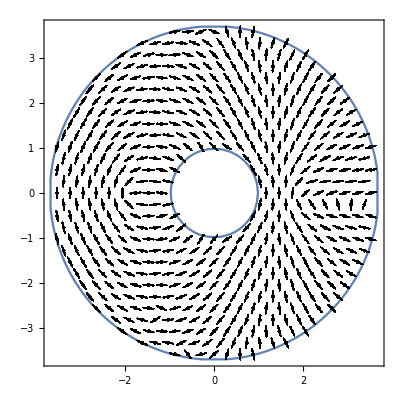

```mathematica
plt=ListVectorPlot[stresses,RegionFunction->Function[{u,v},Rin^2<u^2+v^2<Rout^2],VectorColorFunction->None,VectorStyle->Black,RegionFillingStyle->White,VectorMarkers->"BarDot",VectorPoints->Fine,RegionBoundaryStyle->Bold]
```

```mathematica
Export["principal.bmp",plt,"BMP"]
```